### Sin wave density fitness function

```mathematica
SeedRandom[444110 + 6];
exampleevolution = 
AdaptiveSearch[CellularAutomaton[{0, 4, 1}], 2000,
"MutationFunction"->( RandomRuleMutation[#, 1, "Symmetric"->True]&),
 "FitnessFunction"-> (-Total[Abs[(Count[#, x_/;x>0] / 200&/@ CellularAutomaton[#, {{1}, 0}, {100, {-100, 100}}]) - sf]]&)];
```

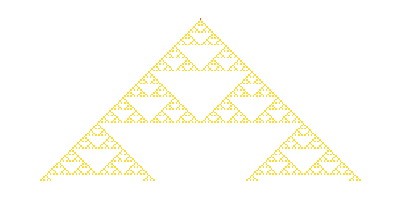
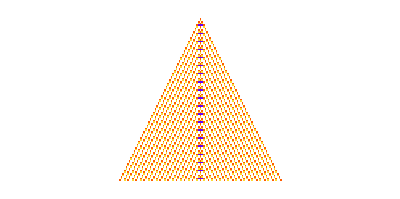
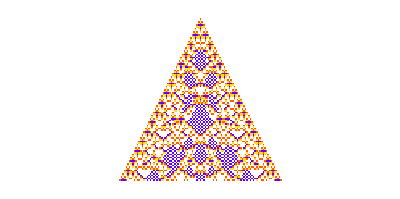
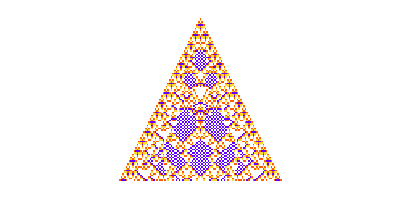
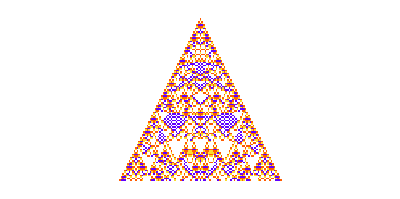
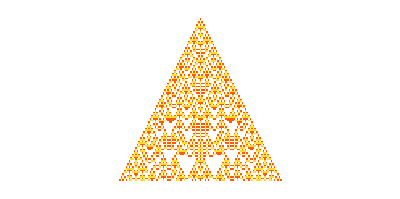
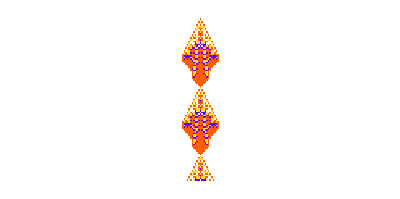
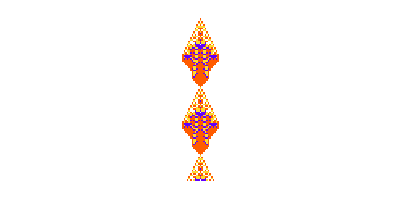
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ArrayPlot[ArrayPad[#, 1]&/@CellularAutomaton[#rule, {{1}, 0}, {100, {-100, 100}}], ImageSize->Automatic]&/@ GatherBy[#, Last][[All, 1]]&@ exampleevolution
```

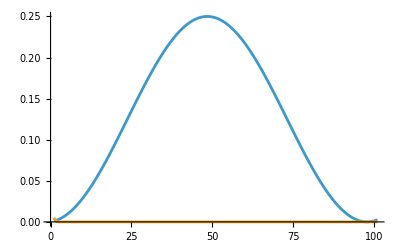
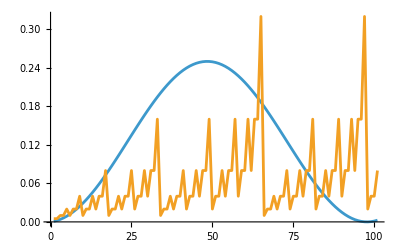
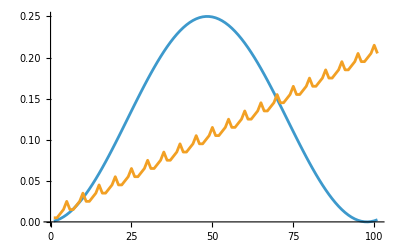
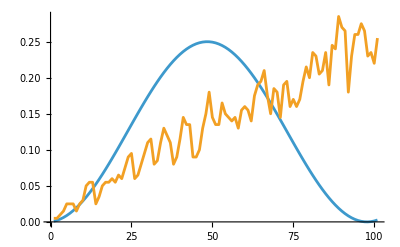
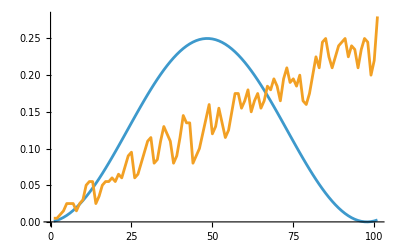
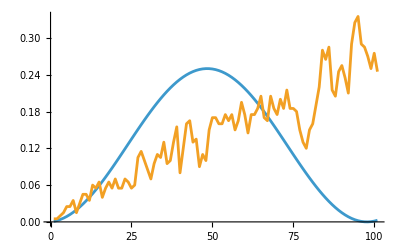
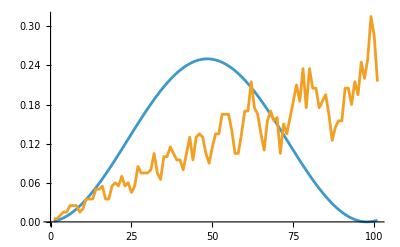
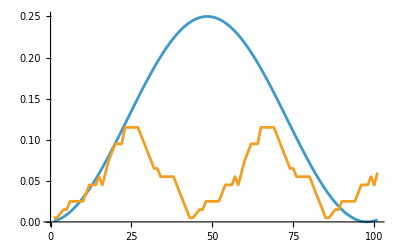

```mathematica
ListLinePlot[{sf, #}]&/@(Count[#, x_/;x>0] / 200&/@ CellularAutomaton[#rule, {{1}, 0}, {100, {-100, 100}}]&)/@ GatherBy[#, Last][[All, 1]]&@ exampleevolution
```

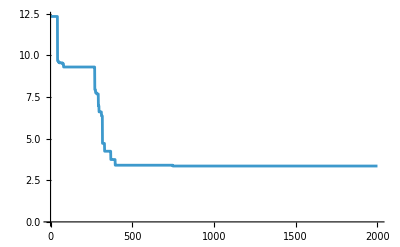

```mathematica
ListLinePlot[-exampleevolution[[All, "fitness"]], PlotRange->All]
```

#### Did not learn to extrapolate yet:

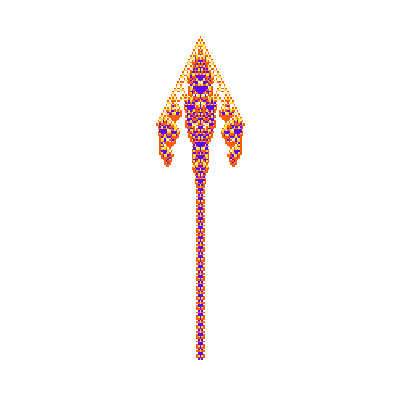

```mathematica
ArrayPlot[ArrayPad[#, 1]&/@CellularAutomaton[#rule, {{1}, 0}, {200, {-100, 100}}], ImageSize->Automatic]&@ GatherBy[#, Last][[-1, 1]]&@ exampleevolution
```

#### Code to run more

```mathematica
searches = ParallelTable[
SeedRandom[444110 + i];
AdaptiveSearch[CellularAutomaton[{0, 4, 1}], 2000,
"MutationFunction"->( RandomRuleMutation[#, 1, "Symmetric"->True]&),
 "FitnessFunction"-> (-Total[Abs[(Count[#, x_/;x>0] / 200&/@ CellularAutomaton[#, {{1}, 0}, {100, {-100, 100}}]) - sf]]&)], {i, 10}];
```